## Akbar’s calculation: Lens photon collection - Comparison to parabolic mirror

### Notes

### Calculating and Plotting the intensity and phase distribution after reflection

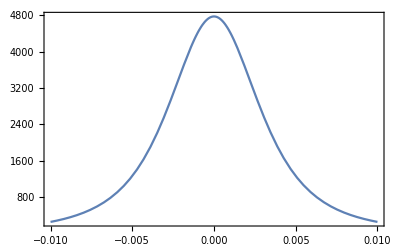

```mathematica
mm=10^-3;
f=5mm;
Eσ2[ρ_]=1/(ρ^2+f^2)3/(16π)f/(√(f^2+ρ^2))(1/(1+ρ^2/f^2)+1);
Plot[Eσ2[ρ],{ρ,-10mm,10mm},PlotRange->All,Frame->True]
```

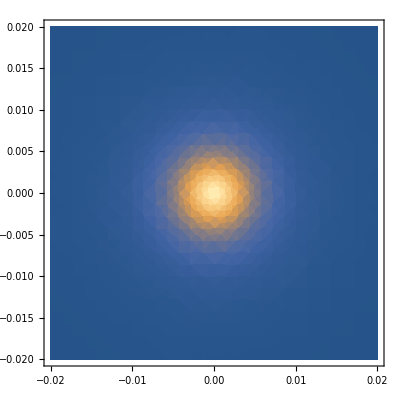

```mathematica
Clear[x,y]
mm=10^-3;
f=5mm;
Eσ2[x_,y_]=1/(x^2+y^2+f^2)3/(16π)f/(√(f^2+x^2+y^2))(1/(1+(x^2+y^2)/f^2)+1); 
DensityPlot[Eσ2[x,y],{x,-20mm,20mm},{y,-20mm,20mm},PlotRange->All,Frame->True]
```

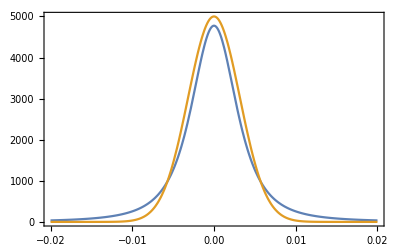

```mathematica
Plot[{Eσ2[x,y=0],5000 ⅇ^(-x^2/0.00002)},{x,-20mm,20mm},PlotRange->All,Frame->True]
```

### Calculating the overlap integral for σ=±1 photons (with the Cos[θ] correction factor) (correct)

Here I am multiplying the field after collimation by √Cos[θ]=√(f/(√(f^2+ρ^2))), such that the intensity of the collimated beam is multiplied by Cos[θ]. This is necessary to get the correct normalization after collimation. Otherwise, the integral that gives the total power after collimation diverges. The explanation is that to find the power contained in a differential surface element of the lens, we need to consider the surface normal to the k-vector. Thus, we need to multiply the intensity by Cos[θ].

```mathematica
Clear["Global`*"]
(* This is the integral we wish to calculate which shows the overlap of a light emitted in a sigma transition and collimated by a lens, with a gaussian beam with arbitrary (but uniform) polarization of α x̂+β ŷ, where α and β are constants (could be complex numbers).  *)
Integrate[ⅇ^(-(ρ/w0)^2)ρ (- ⅈ)/(√(ρ^2+f^2))ⅇ^(-ⅈ ϕ)√(3/(16π))√(f/(√(f^2+ρ^2)))(α (1/(√(1+ρ^2/f^2))Cos[ϕ]+ⅈ Sin[ϕ])+β(1/(√(1+ρ^2/f^2))Sin[ϕ]-ⅈ Cos[ϕ])),{ρ,0,ρ0},{ϕ,0,2π}]
```

$Aborted

```mathematica
(* Breaking the formula into 4 terms to be integrated sperately: *)
- ⅈ √(3/(16π))α ⅇ^(-(ρ/w0)^2)(ρ f)/(ρ^2+f^2)√(f/(√(f^2+ρ^2)))Cos[ϕ] ⅇ^(-ⅈ ϕ)
+ √(3/(16π))α ⅇ^(-(ρ/w0)^2)ρ 1/(√(ρ^2+f^2))√(f/(√(f^2+ρ^2)))Sin[ϕ] ⅇ^(-ⅈ ϕ)
-ⅈ √(3/(16π))β ⅇ^(-(ρ/w0)^2)(ρ f)/(ρ^2+f^2)√(f/(√(f^2+ρ^2)))Sin[ϕ] ⅇ^(-ⅈ ϕ)
- √(3/(16π))β ⅇ^(-(ρ/w0)^2)ρ 1/(√(ρ^2+f^2))√(f/(√(f^2+ρ^2))) Cos[ϕ] ⅇ^(-ⅈ ϕ)
```

```mathematica
(* now calculating the integrals: *)
Clear["Global`*"]
Integrate[Integrate[- ⅈ √(3/(16π))α ⅇ^(-(ρ/w0)^2)(ρ f)/(ρ^2+f^2)√(f/(√(f^2+ρ^2)))Cos[ϕ] ⅇ^(-ⅈ ϕ)
+ √(3/(16π))α ⅇ^(-(ρ/w0)^2)ρ 1/(√(ρ^2+f^2))√(f/(√(f^2+ρ^2)))Sin[ϕ] ⅇ^(-ⅈ ϕ)
-ⅈ √(3/(16π))β ⅇ^(-(ρ/w0)^2)(ρ f)/(ρ^2+f^2)√(f/(√(f^2+ρ^2)))Sin[ϕ] ⅇ^(-ⅈ ϕ)
- √(3/(16π))β ⅇ^(-(ρ/w0)^2)ρ 1/(√(ρ^2+f^2))√(f/(√(f^2+ρ^2)))Cos[ϕ] ⅇ^(-ⅈ ϕ),ρ,Assumptions->{f>0,w0>0}],{ϕ,0,2π},Assumptions->{f>0,w0>0}]
```

(ⅇ^(-ρ^2/w0^2) f √(3 π) (ⅈ α+β) (4 f √w0+ⅇ^((f^2+ρ^2)/w0^2) (f^2+ρ^2)^(1/4) (w0 Gamma[1/4,(f^2+ρ^2)/w0^2]-4 f Gamma[3/4,(f^2+ρ^2)/w0^2])))/(8 √(f w0) (f^2+ρ^2)^(1/4))

```mathematica
(* putting the limits of the integration for ρ: *)
ρ=0;
(ⅇ^(-ρ^2/w0^2) f √(3 π) (ⅈ α+β) (ⅇ^((f^2+ρ^2)/w0^2) w0 (f^2+ρ^2)^(1/4) Gamma[1/4,(f^2+ρ^2)/w0^2]+4 f (√w0-ⅇ^((f^2+ρ^2)/w0^2) (f^2+ρ^2)^(1/4) Gamma[3/4,(f^2+ρ^2)/w0^2])))/(8 √(f w0) (f^2+ρ^2)^(1/4))
```

(f √(3 π) (ⅈ α+β) (ⅇ^(f^2/w0^2) (f^2)^(1/4) w0 Gamma[1/4,f^2/w0^2]+4 f (√w0-ⅇ^(f^2/w0^2) (f^2)^(1/4) Gamma[3/4,f^2/w0^2])))/(8 (f^2)^(1/4) √(f w0))

```mathematica
Clear[ρ]
FullSimplify[(ⅇ^(-ρ^2/w0^2) f √(3 π) (ⅈ α+β) (ⅇ^((f^2+ρ^2)/w0^2) w0 (f^2+ρ^2)^(1/4) Gamma[1/4,(f^2+ρ^2)/w0^2]+4 f (√w0-ⅇ^((f^2+ρ^2)/w0^2) (f^2+ρ^2)^(1/4) Gamma[3/4,(f^2+ρ^2)/w0^2])))/(8 √(f w0) (f^2+ρ^2)^(1/4))-1/(8 (f^2)^(1/4) √(f w0))f √(3 π) (ⅈ α+β) (ⅇ^(f^2/w0^2) (f^2)^(1/4) w0 Gamma[1/4,f^2/w0^2]+4 f (√w0-ⅇ^(f^2/w0^2) (f^2)^(1/4) Gamma[3/4,f^2/w0^2])),Assumptions->{f>0,w0>0}]
```

1/(8 √(f w0))f √(3 π) (ⅈ α+β) (-4 √(f w0)+(4 ⅇ^(-ρ^2/w0^2) f √w0)/((f^2+ρ^2)^(1/4))+ⅇ^(f^2/w0^2) (-w0 Gamma[1/4,f^2/w0^2]+w0 Gamma[1/4,(f^2+ρ^2)/w0^2]+4 f (Gamma[3/4,f^2/w0^2]-Gamma[3/4,(f^2+ρ^2)/w0^2])))

```mathematica
Int=(f √(3 π))/(8 √(f w0)) (ⅈ α+β) (-4 √(f w0)+(4 ⅇ^(-ρ^2/w0^2) f √w0)/((f^2+ρ^2)^(1/4))+ⅇ^(f^2/w0^2) (-w0 Gamma[1/4,f^2/w0^2]+w0 Gamma[1/4,(f^2+ρ^2)/w0^2]+4 f (Gamma[3/4,f^2/w0^2]-Gamma[3/4,(f^2+ρ^2)/w0^2])))
```

1/(8 √(f w0))f √(3 π) (ⅈ α+β) (-4 √(f w0)+(4 ⅇ^(-ρ^2/w0^2) f √w0)/((f^2+ρ^2)^(1/4))+ⅇ^(f^2/w0^2) (-w0 Gamma[1/4,f^2/w0^2]+w0 Gamma[1/4,(f^2+ρ^2)/w0^2]+4 f (Gamma[3/4,f^2/w0^2]-Gamma[3/4,(f^2+ρ^2)/w0^2])))

#### Integral of the G.G for normalization

```mathematica
Clear["Global`*"]
Integrate[ρ (ⅇ^(-(ρ/w0)^2))^2,{ρ,0,∞},{ϕ,0,2π},Assumptions->{w0>0}]
```

(π w0^2)/2

#### Integral of the E.E for normalization

```mathematica
Clear["Global`*"]
Integrate[ρ(√(3/(16π))1/(√(ρ^2+f^2)))^2(f^2/(f^2+ρ^2)+1 )f/(√(f^2+ρ^2)),{ρ,0,∞},{ϕ,0,2π},Assumptions->{f>0}]
```

1/2

#### Putting everything together

```mathematica
(* The E field of the atom was normalized. The Gaussian was missing a simple factor for normalization. Considering these, the final result for the overlap function is the following. Set (-ⅈ α+β)=1 to find the overlap with any uniform polarization state. *)

OverLapInt=(2 2f 3 π)/(64w0 π w0^2) Abs[(ⅈ α+β)]^2 Abs[ (-4 √(f w0)+(4 ⅇ^(-ρ^2/w0^2) f √w0)/((f^2+ρ^2)^(1/4))+ⅇ^(f^2/w0^2) (-w0 Gamma[1/4,f^2/w0^2]+w0 Gamma[1/4,(f^2+ρ^2)/w0^2]+4 f (Gamma[3/4,f^2/w0^2]-Gamma[3/4,(f^2+ρ^2)/w0^2])))]^2
```

1/(16 w0^3)3 f Abs[ⅈ α+β]^2 Abs[-4 √(f w0)+(4 ⅇ^(-ρ^2/w0^2) f √w0)/((f^2+ρ^2)^(1/4))+ⅇ^(f^2/w0^2) (-w0 Gamma[1/4,f^2/w0^2]+w0 Gamma[1/4,(f^2+ρ^2)/w0^2]+4 f (Gamma[3/4,f^2/w0^2]-Gamma[3/4,(f^2+ρ^2)/w0^2]))]^2

### Calculating the overlap integral for σ=±1 photons (with the Cos[θ] correction factor) (as a function of NA)

```mathematica
(* I am replacing ρ by (f NA)/(√(1-NA^2)) *)
Clear["Global`*"]
OverLapInt=(2 2f 3 π)/(64w0 π w0^2) Abs[(ⅈ α+β)]^2 Abs[ (-4 √(f w0)+(4 ⅇ^(-(((f NA)/(√(1-NA^2)))^2)/w0^2) f √w0)/((f^2+((f NA)/(√(1-NA^2)))^2)^(1/4))+ⅇ^(f^2/w0^2) (-w0 Gamma[1/4,f^2/w0^2]+w0 Gamma[1/4,(f^2+((f NA)/(√(1-NA^2)))^2)/w0^2]+4 f (Gamma[3/4,f^2/w0^2]-Gamma[3/4,(f^2+((f NA)/(√(1-NA^2)))^2)/w0^2])))]^2
(* The first factor of two in the numerator comes from the normalization of the field which is 1/2 when integrated over half of the space (where the lens is). So, with this factor of two, we are calculating the coupling efficiency of the photons that are already emitted to the right, where the lens is. To calculate the overal collection efficiency, we should remove this factor of two from the numerator. *)
```

1/(16 w0^3)3 f Abs[ⅈ α+β]^2 Abs[(4 ⅇ^(-(f^2 NA^2)/((1-NA^2) w0^2)) f √w0)/((f^2+(f^2 NA^2)/(1-NA^2))^(1/4))-4 √(f w0)+ⅇ^(f^2/w0^2) (-w0 Gamma[1/4,f^2/w0^2]+w0 Gamma[1/4,(f^2+(f^2 NA^2)/(1-NA^2))/w0^2]+4 f (Gamma[3/4,f^2/w0^2]-Gamma[3/4,(f^2+(f^2 NA^2)/(1-NA^2))/w0^2]))]^2

#### Gaussian waist optimized for each NA

For each value of NA, the coupling efficiency (the overlap integral) depends on the waist of the Gaussian beam we assume. Here I am generating a list of beam waists and calculate the overlap with all of them, and chose the maximum overlap. 

I plotted the coupling efficiency as a function of the beam waist for different values of NA. From the plots, I learned that the optimum efficiency occurs with beam waists around two times the focal length. That is how I chose the range of w0.

I did this for f=2mm and 5mm. The results were exactly the same.

General::munfl: Exp[-1116.37] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1116.48] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1112.86] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

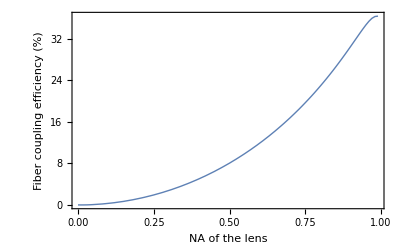

```mathematica
Clear["Global`*"]
mm=10^-3;
f=5mm;
α=1/(√2);
β=ⅈ/(√2);
w0=Range[100]/100 3f;
MaxLensList={};
NAList={};
For[j=0,j<100,j++,
NA=j/100;
MyLensRes=100. (2f 3 π)/(64w0 π w0^2) Abs[(ⅈ α+β)]^2 Abs[ -4 √(f w0)+(4 ⅇ^(-(((f NA)/(√(1-NA^2)))^2)/w0^2) f √w0)/((f^2+((f NA)/(√(1-NA^2)))^2)^(1/4))+ⅇ^(f^2/w0^2) (-w0 Gamma[1/4,f^2/w0^2]+w0 Gamma[1/4,(f^2+((f NA)/(√(1-NA^2)))^2)/w0^2]+4 f (Gamma[3/4,f^2/w0^2]-Gamma[3/4,(f^2+((f NA)/(√(1-NA^2)))^2)/w0^2]))]^2;
MyLensRes=Select[MyLensRes,#<100&];(* for some reason, the first value, corresponding to very low NA, is super large (several thousand). So, I am removing any large values. *)
MaxLens=Max[MyLensRes];
MaxLensList=Append[MaxLensList,MaxLens];
NAList=Append[NAList,NA];
]

MaxLensNAList=Transpose[{NAList,MaxLensList}];

ListPlot[MaxLensNAList,Frame->True,PlotRange->All,Joined->True,PlotStyle->Thick,FrameStyle->Directive[Black,14],FrameLabel->{"NA of the lens","Fiber coupling efficiency (%)"}]
```

## Modification to account for finite temperature:

### Calculating the overlap integral for σ=±1 photons (with the Cos[θ] correction factor) (correct)

Here I am multiplying the field after collimation by √Cos[θ]=√(f/(√(f^2+ρ^2))), such that the intensity of the collimated beam is multiplied by Cos[θ]. This is necessary to get the correct normlization after collimation. Otherwise, the integral that gives the total power after collimation diverges. The explanation is that to find the power contained in a differential surface element of the lens, we need to consider the surface normal to the k-vector. Thus, we need to multiply the intensity by Cos[θ].

```mathematica
Clear["Global`*"]
(* This is the integral we wish to calculate which shows the overlap of a light emitted in a sigma transition and collimated by a lens, with a gaussian beam with arbitrary (but uniform) polarization of α x̂+β ŷ, where α and β are constants (could be complex numbers).  *)
Integrate[ⅇ^(-(ρ/w0)^2)ρ (- ⅈ)/(√(ρ^2+f^2))ⅇ^(-ⅈ ϕ)√(3/(16π))√(f/(√(f^2+ρ^2)))(α (1/(√(1+ρ^2/f^2))Cos[ϕ]+ⅈ Sin[ϕ])+β(1/(√(1+ρ^2/f^2))Sin[ϕ]-ⅈ Cos[ϕ])),{ρ,0,ρ0},{ϕ,0,2π}]
```

$Aborted

```mathematica
(* Breaking the formula into 4 terms to be integrated sperately: *)
- ⅈ √(3/(16π))α ⅇ^(-(ρ/w0)^2)(ρ f)/(ρ^2+f^2)√(f/(√(f^2+ρ^2)))Cos[ϕ] ⅇ^(-ⅈ ϕ)
+ √(3/(16π))α ⅇ^(-(ρ/w0)^2)ρ 1/(√(ρ^2+f^2))√(f/(√(f^2+ρ^2)))Sin[ϕ] ⅇ^(-ⅈ ϕ)
-ⅈ √(3/(16π))β ⅇ^(-(ρ/w0)^2)(ρ f)/(ρ^2+f^2)√(f/(√(f^2+ρ^2)))Sin[ϕ] ⅇ^(-ⅈ ϕ)
- √(3/(16π))β ⅇ^(-(ρ/w0)^2)ρ 1/(√(ρ^2+f^2))√(f/(√(f^2+ρ^2))) Cos[ϕ] ⅇ^(-ⅈ ϕ)
```

```mathematica
(* now calculating the integrals: *)
Clear["Global`*"]
Integrate[Integrate[- ⅈ √(3/(16π))α ⅇ^(-(ρ/w0)^2)(ρ f)/(ρ^2+f^2)√(f/(√(f^2+ρ^2)))Cos[ϕ] ⅇ^(-ⅈ ϕ)
+ √(3/(16π))α ⅇ^(-(ρ/w0)^2)ρ 1/(√(ρ^2+f^2))√(f/(√(f^2+ρ^2)))Sin[ϕ] ⅇ^(-ⅈ ϕ)
-ⅈ √(3/(16π))β ⅇ^(-(ρ/w0)^2)(ρ f)/(ρ^2+f^2)√(f/(√(f^2+ρ^2)))Sin[ϕ] ⅇ^(-ⅈ ϕ)
- √(3/(16π))β ⅇ^(-(ρ/w0)^2)ρ 1/(√(ρ^2+f^2))√(f/(√(f^2+ρ^2)))Cos[ϕ] ⅇ^(-ⅈ ϕ),ρ,Assumptions->{f>0,w0>0}],{ϕ,0,2π},Assumptions->{f>0,w0>0}]
```

(ⅇ^(-ρ^2/w0^2) f √(3 π) (ⅈ α+β) (ⅇ^((f^2+ρ^2)/w0^2) w0 (f^2+ρ^2)^(1/4) Gamma[1/4,(f^2+ρ^2)/w0^2]+4 f (√w0-ⅇ^((f^2+ρ^2)/w0^2) (f^2+ρ^2)^(1/4) Gamma[3/4,(f^2+ρ^2)/w0^2])))/(8 √(f w0) (f^2+ρ^2)^(1/4))

```mathematica
(* putting the limits of the integration for ρ: *)
ρ=0;
(ⅇ^(-ρ^2/w0^2) f √(3 π) (ⅈ α+β) (ⅇ^((f^2+ρ^2)/w0^2) w0 (f^2+ρ^2)^(1/4) Gamma[1/4,(f^2+ρ^2)/w0^2]+4 f (√w0-ⅇ^((f^2+ρ^2)/w0^2) (f^2+ρ^2)^(1/4) Gamma[3/4,(f^2+ρ^2)/w0^2])))/(8 √(f w0) (f^2+ρ^2)^(1/4))
```

(f √(3 π) (ⅈ α+β) (ⅇ^(f^2/w0^2) (f^2)^(1/4) w0 Gamma[1/4,f^2/w0^2]+4 f (√w0-ⅇ^(f^2/w0^2) (f^2)^(1/4) Gamma[3/4,f^2/w0^2])))/(8 (f^2)^(1/4) √(f w0))

```mathematica
Clear[ρ]
FullSimplify[(ⅇ^(-ρ^2/w0^2) f √(3 π) (ⅈ α+β) (ⅇ^((f^2+ρ^2)/w0^2) w0 (f^2+ρ^2)^(1/4) Gamma[1/4,(f^2+ρ^2)/w0^2]+4 f (√w0-ⅇ^((f^2+ρ^2)/w0^2) (f^2+ρ^2)^(1/4) Gamma[3/4,(f^2+ρ^2)/w0^2])))/(8 √(f w0) (f^2+ρ^2)^(1/4))-(f √(3 π) (ⅈ α+β) (ⅇ^(f^2/w0^2) (f^2)^(1/4) w0 Gamma[1/4,f^2/w0^2]+4 f (√w0-ⅇ^(f^2/w0^2) (f^2)^(1/4) Gamma[3/4,f^2/w0^2])))/(8 (f^2)^(1/4) √(f w0)),Assumptions->{f>0,w0>0}]
```

(f √(3 π) (ⅈ α+β) (-4 √(f w0)+(4 ⅇ^(-ρ^2/w0^2) f √w0)/((f^2+ρ^2)^(1/4))+ⅇ^(f^2/w0^2) (-w0 Gamma[1/4,f^2/w0^2]+w0 Gamma[1/4,(f^2+ρ^2)/w0^2]+4 f (Gamma[3/4,f^2/w0^2]-Gamma[3/4,(f^2+ρ^2)/w0^2]))))/(8 √(f w0))

```mathematica
Int=(f √(3 π))/(8 √(f w0)) (ⅈ α+β) (-4 √(f w0)+(4 ⅇ^(-ρ^2/w0^2) f √w0)/((f^2+ρ^2)^(1/4))+ⅇ^(f^2/w0^2) (-w0 Gamma[1/4,f^2/w0^2]+w0 Gamma[1/4,(f^2+ρ^2)/w0^2]+4 f (Gamma[3/4,f^2/w0^2]-Gamma[3/4,(f^2+ρ^2)/w0^2])))
```

#### Integral of the G.G for normalization

```mathematica
Clear["Global`*"]
Integrate[ρ (ⅇ^(-(ρ/w0)^2))^2,{ρ,0,∞},{ϕ,0,2π},Assumptions->{w0>0}]
```

(π w0^2)/2

#### Integral of the E.E for normalization

```mathematica
Clear["Global`*"]
Integrate[ρ(√(3/(16π))1/(√(ρ^2+f^2)))^2(f^2/(f^2+ρ^2)+1 )f/(√(f^2+ρ^2)),{ρ,0,∞},{ϕ,0,2π},Assumptions->{f>0}]
```

1/2

#### Putting everything together

```mathematica
(* The E field of the atom was normalized. The Gaussian was missing a simple factor for normalization. Considering these, the final result for the overlap function is the following. Set (-ⅈ α+β)=1 to find the overlap with any uniform polarization state. *)

OverLapInt=(2 2f 3 π)/(64w0 π w0^2) Abs[(ⅈ α+β)]^2 Abs[ (-4 √(f w0)+(4 ⅇ^(-ρ^2/w0^2) f √w0)/((f^2+ρ^2)^(1/4))+ⅇ^(f^2/w0^2) (-w0 Gamma[1/4,f^2/w0^2]+w0 Gamma[1/4,(f^2+ρ^2)/w0^2]+4 f (Gamma[3/4,f^2/w0^2]-Gamma[3/4,(f^2+ρ^2)/w0^2])))]^2
```

### Calculating the overlap integral for σ=±1 photons (with the Cos[θ] correction factor) (as a function of NA)

```mathematica
(* I am replacing ρ by (f NA)/(√(1-NA^2)) *)
Clear["Global`*"]
OverLapInt=(2 2f 3 π)/(64w0 π w0^2) Abs[(ⅈ α+β)]^2 Abs[ (-4 √(f w0)+(4 ⅇ^(-(((f NA)/(√(1-NA^2)))^2)/w0^2) f √w0)/((f^2+((f NA)/(√(1-NA^2)))^2)^(1/4))+ⅇ^(f^2/w0^2) (-w0 Gamma[1/4,f^2/w0^2]+w0 Gamma[1/4,(f^2+((f NA)/(√(1-NA^2)))^2)/w0^2]+4 f (Gamma[3/4,f^2/w0^2]-Gamma[3/4,(f^2+((f NA)/(√(1-NA^2)))^2)/w0^2])))]^2
(* The first factor of two in the numerator comes from the normalization of the field which is 1/2 when integrated over half of the space (where the lens is). So, with this factor of two, we are calculating the coupling efficiency of the photons that are already emitted to the right, where the lens is. To calculate the overal collection efficiency, we should remove this factor of two from the numerator. *)
```

(3 f Abs[ⅈ α+β]^2 Abs[(4 ⅇ^(-(f^2 NA^2)/((1-NA^2) w0^2)) f √w0)/((f^2+(f^2 NA^2)/(1-NA^2))^(1/4))-4 √(f w0)+ⅇ^(f^2/w0^2) (-w0 Gamma[1/4,f^2/w0^2]+w0 Gamma[1/4,(f^2+(f^2 NA^2)/(1-NA^2))/w0^2]+4 f (Gamma[3/4,f^2/w0^2]-Gamma[3/4,(f^2+(f^2 NA^2)/(1-NA^2))/w0^2]))]^2)/(16 w0^3)

#### Gaussian waist optimized for each NA

For each value of NA, the coupling efficiency (the overlap integral) depends on the waist of the Gaussian beam we assume. Here I am generating a list of beam waists and calculate the overlap with all of them, and chose the maximum overlap. 

I plotted the coupling efficiency as a function of the beam waist for different values of NA. From the plots, I learned that the optimum efficiency occurs with beam waists around two times the focal length. That is how I chose the range of w0.

I did this for f=2mm and 5mm. The results were exactly the same.

```mathematica
Clear["Global`*"]
mm=10^-3;
f=5mm;
α=1/(√2);
β=ⅈ/(√2);
w0=Range[100]/100 3f;
MaxLensList={};
NAList={};
For[j=0,j<100,j++,
NA=j/100;
MyLensRes=100. (2f 3 π)/(64w0 π w0^2) Abs[(ⅈ α+β)]^2 Abs[ -4 √(f w0)+(4 ⅇ^(-(((f NA)/(√(1-NA^2)))^2)/w0^2) f √w0)/((f^2+((f NA)/(√(1-NA^2)))^2)^(1/4))+ⅇ^(f^2/w0^2) (-w0 Gamma[1/4,f^2/w0^2]+w0 Gamma[1/4,(f^2+((f NA)/(√(1-NA^2)))^2)/w0^2]+4 f (Gamma[3/4,f^2/w0^2]-Gamma[3/4,(f^2+((f NA)/(√(1-NA^2)))^2)/w0^2]))]^2;
MyLensRes=Select[MyLensRes,#<100&];(* for some reason, the first value, corresponding to very low NA, is super large (several thousand). So, I am removing any large values. *)
MaxLens=Max[MyLensRes];
MaxLensList=Append[MaxLensList,MaxLens];
NAList=Append[NAList,NA];

]

MaxLensNAList=Transpose[{NAList,MaxLensList}];

ListPlot[MaxLensNAList,Frame->True,PlotRange->All,Joined->True,PlotStyle->Thick,FrameStyle->Directive[Black,14],FrameLabel->{"NA of the lens","Fiber coupling efficiency (%)"}]
```

General::munfl: Exp[-1116.37] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1116.48] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1112.86] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-